```mathematica
i={{1,0},{0,1}};
x={{0,1},{1,0}};
y={{0,-I},{I,0}};
z={{1,0},{0,-1}};
h0=-Rationalize[0.08496]i-Rationalize[0.89134]x+Rationalize[0.26536]y+Rationalize[0.57205]z;
h1=-Rationalize[0.84537]i+Rationalize[0.00673]x-Rationalize[0.29354]y+Rationalize[0.18477]z;
eigsystem=Eigensystem[h0+φ*h1];
eigvals=eigsystem[[1]];
eigvecs=Table[Normalize[eigsystem[[2]][[k]]],{k,2}];
initialState=Normalize[{1,0}];
probAllZeroExpectation=Sum[Abs[initialState.eigvecs[[k]]]^2(1/2(1+ⅇ^(-1/2 σ^2(ℰ-eigvals[[k]])^2)))^n,{k,2}];
```

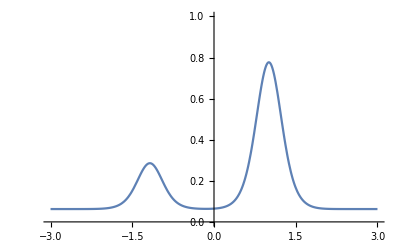

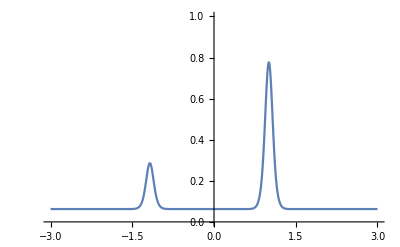

```mathematica
Plot[probAllZeroExpectation/.{φ->0,n->4,σ->3},{ℰ,-3,3},PlotRange->{0,1}]
Plot[probAllZeroExpectation/.{φ->0,n->4,σ->10},{ℰ,-3,3},PlotRange->{0,1}]
```

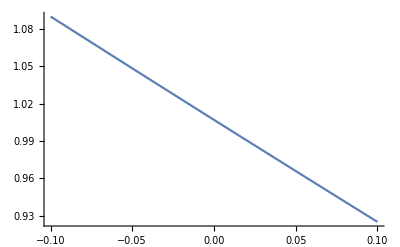

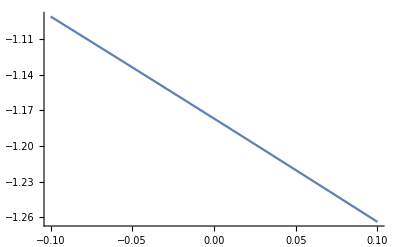

```mathematica
Plot[eigvals[[2]],{φ,-1/10,1/10}]
Plot[eigvals[[1]],{φ,-1/10,1/10}]
```